# L1000 Peak Deconvolution

## Load Function

```mathematica
$libpath=NotebookDirectory[]<>"/../src/dpeak.so";
wllcudadpeak=LibraryFunctionLoad[$libpath,"wll_cudadpeak",
{{Real,2,"Constant"},{Real,1,"Constant"},{Real,1,"Constant"},{Real,2,"Constant"}, {Real,1,"Constant"}},{Real,3}];
```

## Test Peak Deconvolution

The mock distribution is a mixture (2:1) of two normal distributions, centered at 7.3 and 9.4.

```mathematica
peaksdist=MixtureDistribution[{0.667,0.333},{NormalDistribution[7.3,0.27],NormalDistribution[9.4,0.19]}];
```

The background is obtained by all reads in the well in real data, but we use a uniform distribution for simplicity here.

```mathematica
background=UniformDistribution[{2.,14.}];
```

40 reads are sampled from a mixture distribution of the peaks and the background with a misidentification rate (α_c) of 5%.

```mathematica
reads=RandomVariate[MixtureDistribution[{0.95,0.05},{peaksdist,background}],40];
```

Calculate the probability of being a misidentified bead at the values of all reads.

```mathematica
bgprob=PDF[background,reads];
```

The grid of all possible peak locations for likelihood calculation.

```mathematica
grid=Range[2.0,14.0,0.04];
```

Calculate the log-likelihood function.

```mathematica
likelihood=wllcudadpeak[{reads},{0.667},{0.05},{bgprob},grid][[1]];
```

The marginal distributions of the locations of two peaks.

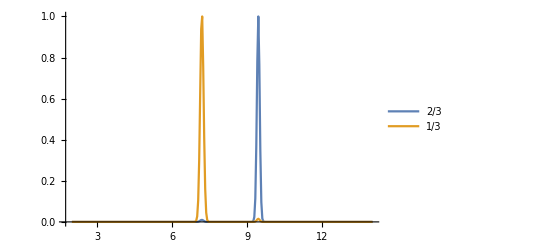

```mathematica
ListLinePlot[Table[Transpose@{grid,#/Max[#]&@Total[Exp@likelihood,{i}]},{i,2}],PlotRange->All,PlotLegends->{"2/3","1/3"}]
```